```mathematica
ϵ=10^-5;
nself[u_,vesc_]:=1+Log[(u^2+vesc^2)/vesc^2]/Log[Log[1/ϵ]];(*all velocities are in km/sec*)
```

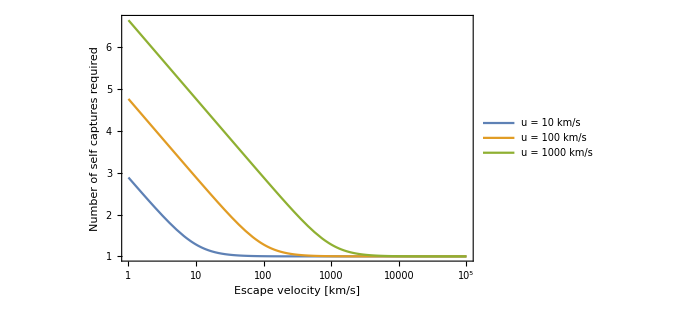

```mathematica
plot1=LogLinearPlot[{nself[10,vesc],nself[100,vesc],nself[1000,vesc]},{vesc,1,10^5},Frame->True,PlotRange->All,FrameLabel->{Style["Escape velocity [km/s] ",FontSize->14,Bold],Style["Number of self captures required",FontSize->14,Bold]},FrameStyle->Directive[14, "Times",Black],PlotLegends -> Placed[{"u = 10 km/s","u = 100 km/s","u = 1000 km/s"},Top],ImageSize->500]
```

```mathematica
Export["plot1.pdf",plot1];
```